```mathematica
T0mat[h_]={{-2/h^3,1/h^2,1/h^2},
{3/h^2,-2/h,-1/h},
{0,1,0}};
Tmat[i_,h_]={{(-1+2 i)/(h^4 i^2),(-3-2 i)/(h^4 (1+i)^2),1/(h^3 i),1/(h^3 (1+i))},
{(2-6 i^2)/(h^3 i^2),(2 (2+6 i+3 i^2))/(h^3 (1+i)^2),-(2+3 i)/(h^2 i),(-1-3 i)/(h^2 (1+i))},
{((1+i) (-1-3 i+6 i^2))/(h^2 i^2),-(i (8+15 i+6 i^2))/(h^2 (1+i)^2),((1+i) (1+3 i))/(h i),(i (2+3 i))/(h (1+i))},
{-(2 (-1+i) (1+i)^2)/(h i),(2 i^2 (2+i))/(h (1+i)),-(1+i)^2,-i^2}};
```

```mathematica
Pbar[i_,h_]:={{-2/9 h^9 i^9+2/9 h^9 (1+i)^9,1/4 (-h^8 i^8+h^8 (1+i)^8),2/7 (-h^7 i^7+h^7 (1+i)^7),1/3 (-h^6 i^6+h^6 (1+i)^6)},
{1/4 (-h^8 i^8+h^8 (1+i)^8),2/7 (-h^7 i^7+h^7 (1+i)^7),1/3 (-h^6 i^6+h^6 (1+i)^6),2/5 (-h^5 i^5+h^5 (1+i)^5)},
{2/7 (-h^7 i^7+h^7 (1+i)^7),1/3 (-h^6 i^6+h^6 (1+i)^6),2/5 (-h^5 i^5+h^5 (1+i)^5),1/2 (-h^4 i^4+h^4 (1+i)^4)},
{1/3 (-h^6 i^6+h^6 (1+i)^6),2/5 (-h^5 i^5+h^5 (1+i)^5),1/2 (-h^4 i^4+h^4 (1+i)^4),2/3 (-h^3 i^3+h^3 (1+i)^3)}}
```

```mathematica
Qbar[i_,h_]:={{24/7 (-h^7 i^7+h^7 (1+i)^7)+1/2 (-h^8 i^8+h^8 (1+i)^8),2 (-h^6 i^6+h^6 (1+i)^6)+4/7 (-h^7 i^7+h^7 (1+i)^7),4/5 (-h^5 i^5+h^5 (1+i)^5)+2/3 (-h^6 i^6+h^6 (1+i)^6),4/5 (-h^5 i^5+h^5 (1+i)^5)},
{4 (-h^6 i^6+h^6 (1+i)^6)+4/7 (-h^7 i^7+h^7 (1+i)^7),12/5 (-h^5 i^5+h^5 (1+i)^5)+2/3 (-h^6 i^6+h^6 (1+i)^6),-h^4 i^4+h^4 (1+i)^4+4/5 (-h^5 i^5+h^5 (1+i)^5),-h^4 i^4+h^4 (1+i)^4},
{24/5 (-h^5 i^5+h^5 (1+i)^5)+2/3 (-h^6 i^6+h^6 (1+i)^6),3 (-h^4 i^4+h^4 (1+i)^4)+4/5 (-h^5 i^5+h^5 (1+i)^5),-h^4 i^4+h^4 (1+i)^4+4/3 (-h^3 i^3+h^3 (1+i)^3),4/3 (-h^3 i^3+h^3 (1+i)^3)},
{6 (-h^4 i^4+h^4 (1+i)^4)+4/5 (-h^5 i^5+h^5 (1+i)^5),-h^4 i^4+h^4 (1+i)^4+4 (-h^3 i^3+h^3 (1+i)^3),2 (-h^2 i^2+h^2 (1+i)^2)+4/3 (-h^3 i^3+h^3 (1+i)^3),2 (-h^2 i^2+h^2 (1+i)^2)}}
```

```mathematica
(* make the entire P or Q matrix *)
makePorQ[N_,PorQbar_,tail_]:=Module[{h=1/N,res=ConstantArray[0,{2N,2N}]},
(* deal with the head, i=0 *)
Tmat0=T0mat[h];PorQbar0=PorQbar[0,h][[{2,3,4},{2,3,4}]];
res[[{1,N+1,N+2},{1,N+1,N+2}]]=Transpose[Tmat0].PorQbar0.Tmat0;
(* deal with the body, 0<i<N-1 *)
Do[Tmati=Tmat[i,h];PorQbari=PorQbar[i,h];
res[[{i,i+1,N+i+1,N+i+2},{i,i+1,N+i+1,N+i+2}]]+=Transpose[Tmati].PorQbari.Tmati,{i,1,N-2}];
(* deal with the tail, i=N-1 *)
Tmatt=Tmat[N-1,h];PorQbart=PorQbar[N-1,h];
res[[{N-1,N,2N},{N-1,N,2N}]]=(Transpose[Tmatt].PorQbart.Tmatt)[[{1,2,3},{1,2,3}]];
(* deal with the actual tail, i=N *)
res[[N,N]]+=tail;
res]
```

```mathematica
ψexact[r_]:=2r Exp[-r];
ψq[D_,C_,B_,A_,r_]:=D r+C r^2+B r^3+A r^4; (* q: quartic *)
ψt[rN_,ψN_,r_]:=ψN r/rN Exp[1-r/rN];(* t: tail *)
```

```mathematica
(* integrate the square of a function in an interval *)
intsqq[D_,C_,B_,A_,r0_,rh_]:=-1/3 D^2 r0^3-1/2 C D r0^4-(C^2 r0^5)/5-2/5 B D r0^5-1/3 B C r0^6-1/3 A D r0^6-(B^2 r0^7)/7-2/7 A C r0^7-1/4 A B r0^8-(A^2 r0^9)/9+(D^2 rh^3)/3+1/2 C D rh^4+(C^2 rh^5)/5+2/5 B D rh^5+1/3 B C rh^6+1/3 A D rh^6+(B^2 rh^7)/7+2/7 A C rh^7+1/4 A B rh^8+(A^2 rh^9)/9;
(* integrate the square of a function in the tail *)
(* Integrate[ψtail[rN,ψN,r]^2,{r,rN,Infinity},Assumptions->rN>0] *)
intsqt[rN_,ψN_]:=(5 rN ψN^2)/4;
```

```mathematica
normalN[ψ_,N_]:=Module[{h=1/N},res=0;
(* deal with the head, i=0 *)
{BB,CC,DD}=T0mat[h].ψ[[{1,N+1,N+2}]];
res+=intsqq[DD,CC,BB,0,0,h];
(* deal with the body, 0<i<N-1 *)
Do[{AA,BB,CC,DD}=Tmat[i,h].ψ[[{i,i+1,N+i+1,N+i+2}]];
res+=intsqq[DD,CC,BB,AA,i h,(i+1)h],{i,1,N-2}];
(* deal with the tail, i=N-1 *)
{AA,BB,CC,DD}=Tmat[N-1,h].(Join[ψ[[{N-1,N,2N}]],{0}]);
res+=intsqq[DD,CC,BB,AA,(N-1) h,1];
(* deal with the actual tail, i=N *)
res+=intsqt[1,ψ[[1]]];
1/Sqrt[res]];
```

```mathematica
renderN[ψ_,N_,r_]:=Module[{i=IntegerPart[r*N],h=1/N},
If[i≥N,res=ψt[1,ψ[[N]],r],];
If[i==0,{BB,CC,DD}=T0mat[h].ψ[[{1,N+1,N+2}]];res=ψq[DD,CC,BB,0,r],];
If[0<i<N-1,{AA,BB,CC,DD}=Tmat[i,h].ψ[[{i,i+1,N+i+1,N+i+2}]];
res=ψq[DD,CC,BB,AA,r],];
If[i==N-1,{AA,BB,CC,DD}=Tmat[N-1,h].(Join[ψ[[{N-1,N,2N}]],{0}]);
res=ψq[DD,CC,BB,AA,r]];
res]
```

```mathematica
(* N = 1 case *)
normal1[ψ_,hh_,Tmat1_]:=Module[{},res=0;
{BB,CC,DD}=Tmat1.ψ;
res+=intsqq[DD,CC,BB,0,0,hh];
res+=intsqt[hh,ψ[[1]]];
1/Sqrt[res]];
render1[ψ_,hh_,Tmat1_,r_]:=If[r≤hh,{BB,CC,DD}=Tmat1.ψ;res=ψq[DD,CC,BB,0,r],res=ψt[hh,ψ[[1]],r]]
```

```mathematica
hh=1
```

1

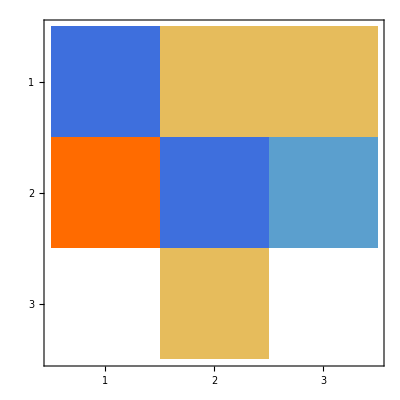

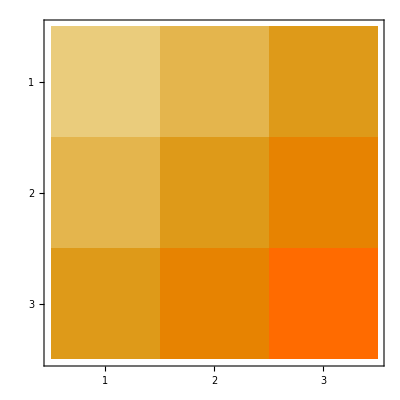

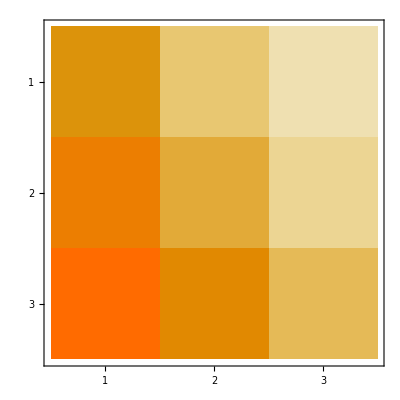

```mathematica
Tmat1=T0mat[hh];
MatrixPlot[Tmat1]
Pbar1=Pbar[0,hh][[{2,3,4},{2,3,4}]];
(*Pbar1[[1,1]]+=(5/2)*hh;*)
MatrixPlot[Pbar1]
Qbar1=Qbar[0,hh][[{2,3,4},{2,3,4}]];
(*Qbar1[[1,1]]+=3-1/(2hh);*)
MatrixPlot[Qbar1]
```

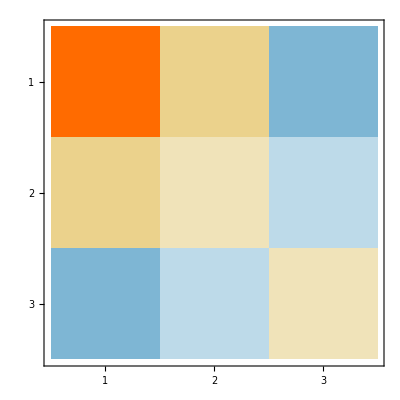

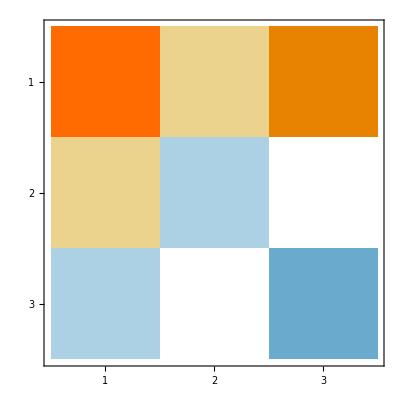

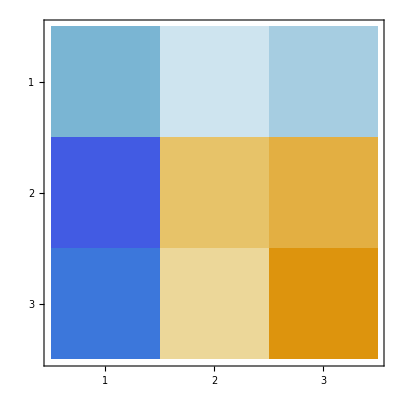

```mathematica
PP1=Transpose[Tmat1].Pbar1.Tmat1;
PP1[[1,1]]+=(5/2)*hh;
MatrixPlot[PP1]
QQ1=Transpose[Tmat1].Qbar1.Tmat1;
QQ1[[1,1]]+=3-1/(2hh);
MatrixPlot[QQ1]
HH1=-Inverse[PP1].QQ1;MatrixPlot[HH1]
```

{{34.21197067168716,4.607203245860952,-1.034363790965832},{{-0.005131226578262045,0.6994569331495468,0.7146563294219348},{-0.005330219862021083,-0.8495828205505953,0.5274283077172835},{0.3544725643874011,0.9347936850110879,0.02258246133641761}}}

{0.73683385834461,1.9431338469685,0.046941636078907}

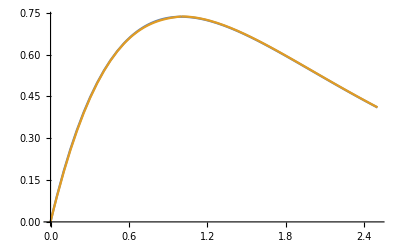

```mathematica
HH1=-Inverse[PP1].QQ1;
{EE1,ψψ1}=Eigensystem[N[HH1,16]]
E1=EE1[[-1]];ψ1=ψψ1[[-1]];
ψ1*=Sign[ψ1[[1]]];ψ1*=normal1[ψ1,hh,Tmat1]
Plot[{ψexact[r],render1[ψ1,hh,T0mat[hh],r]},{r,0,5/2}]
```

```mathematica
solveN1varh[hh_]:=Module[{},
Tmat1=T0mat[hh];
Pbar1=Pbar[0,hh][[{2,3,4},{2,3,4}]];
(*Pbar1[[1,1]]+=(5/2)*hh;*)
Qbar1=Qbar[0,hh][[{2,3,4},{2,3,4}]];
(*Qbar1[[1,1]]+=3-1/(2hh);*)
PP1=Transpose[Tmat1].Pbar1.Tmat1;
PP1[[1,1]]+=(5/2)*hh;
QQ1=Transpose[Tmat1].Qbar1.Tmat1;
QQ1[[1,1]]+=3-1/(2hh);
HH1=-Inverse[PP1].QQ1;
{EE1,ψψ1}=Eigensystem[N[HH1,16]];
E1=EE1[[-1]];ψ1=ψψ1[[-1]];
ψ1*=Sign[ψ1[[1]]];ψ1*=normal1[ψ1,hh,Tmat1];
{E1,ψ1}]
```

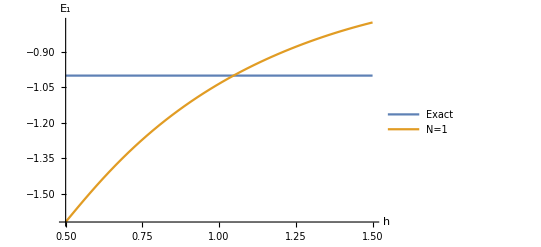

```mathematica
Plot[{-1,solveN1varh[hh][[1]]},{hh,1/2,3/2},
AxesLabel->{h,Subscript["E",1]},
PlotLegends->Placed[{"Exact","N=1"},{Right,Center}]]
```

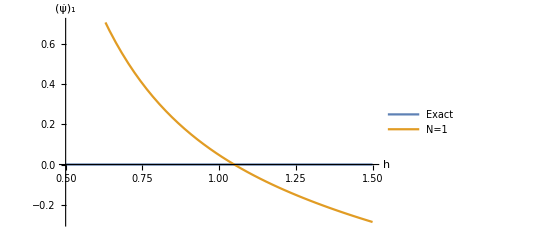

```mathematica
Plot[{0,solveN1varh[hh][[2,-1]]},{hh,1/2,3/2},AxesLabel->{h,Subscript[OverDot[ψ],1]},PlotLegends->Placed[{"Exact","N=1"},{Right,Top}]]
```

```mathematica
{E112,ψ112}=solveN1varh[1/2];
{E134,ψ134}=solveN1varh[3/4];
{E111,ψ111}=solveN1varh[1];
{E154,ψ154}=solveN1varh[5/4];
{E132,ψ132}=solveN1varh[3/2];
```

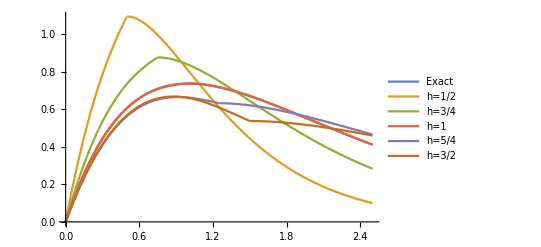

```mathematica
Plot[{ψexact[r],render1[ψ112,1/2,T0mat[1/2],r],
render1[ψ134,3/4,T0mat[3/4],r],
render1[ψ111,1,T0mat[1],r],
render1[ψ154,5/4,T0mat[5/4],r],
render1[ψ132,3/2,T0mat[3/2],r]},{r,0,5/2},PlotLegends->Placed[LineLegend[{"Exact","h=1/2","h=3/4","h=1","h=5/4","h=3/2"},LegendLayout->{"Column",2}],{Right,Top}]]
```

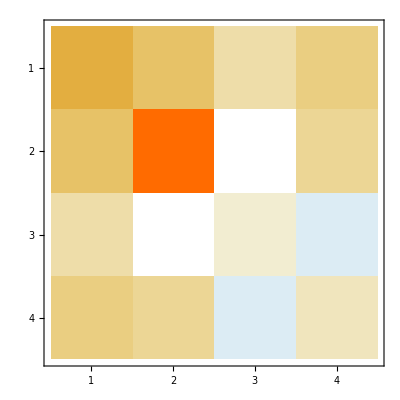

```mathematica
(* N = 2 case *)
PP2=makePorQ[2,Pbar,5/2];
MatrixPlot[PP2]
```

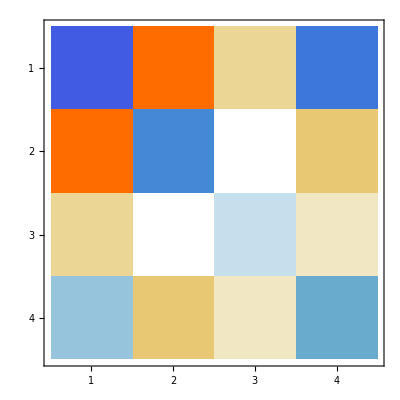

```mathematica
QQ2=makePorQ[2,Qbar,5/2];
MatrixPlot[QQ2]
```

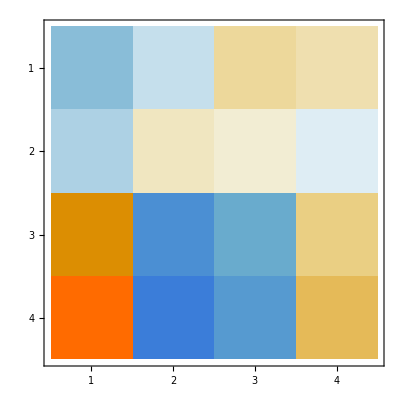

```mathematica
HH2=-Inverse[PP2].QQ2;
MatrixPlot[HH2]
```

```mathematica
{EE2,ψψ2}=Eigensystem[N[HH2,16]];
EE2
ψψ2
```

{37.38836971686025,-37.24233024272227,5.429013703557837,-1.4398614687125}

{{0.05593214445731016,-0.01580565336541418,0.2974433125280617,0.9529686523545424},{0.1622331515353896,0.003889196365251304,-0.5654530550113302,-0.8086582227819621},{0.2032072065950932,-0.0809245567874454,0.959993958324919,-0.1748417778342127},{0.2879268813305553,0.2642780837254792,0.9009646548335525,0.1884619224413956}}

{0.7127180257897,0.6541791208305,2.230197288742,0.4665080546778}

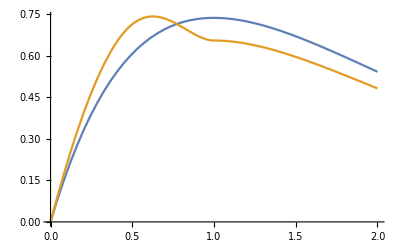

```mathematica
ψ2=normalN[ψψ2[[-1]],2]*ψψ2[[-1]]
Plot[{ψexact[r],renderN[ψ2,2,r]},{r,0,2}]
```

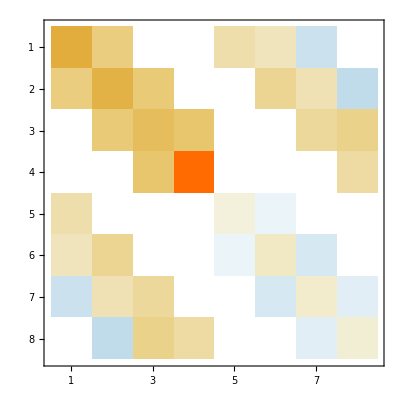

```mathematica
(* N = 4 case *)
PP4=makePorQ[4,Pbar,5/2];
MatrixPlot[PP4]
```

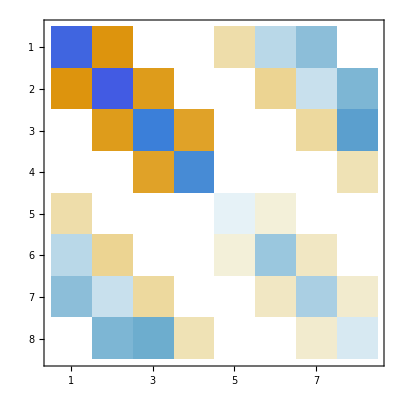

```mathematica
QQ4=makePorQ[4,Qbar,5/2];
MatrixPlot[QQ4]
```

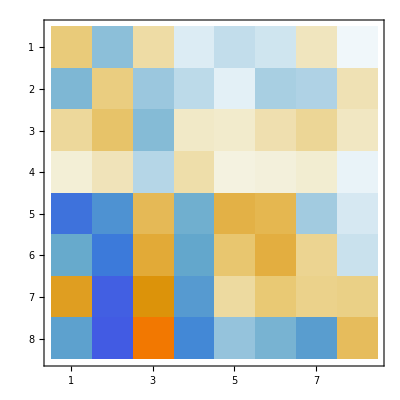

```mathematica
HH4=-Inverse[PP4].QQ4;
MatrixPlot[HH4]
```

```mathematica
{EE4,ψψ4}=Eigensystem[N[HH4,16]];
EE4
ψψ4
```

{508.2185917099646,268.5223515979343,175.6950598568869,133.7780705189706,-93.19037251238786,-42.40936867518079,32.53126603131462,2.329738428516163}

{{0.00936953887575053,0.01170091703630389,-0.00404978075774878,-0.0002056812535013706,-0.8073018369773075,-0.5358956311362723,-0.1627899573110703,0.1853048936039808},{-0.01725741582958275,0.02260250253549806,-0.00103485771188026,-0.001395752703431195,0.6028470610874244,-0.2006677244231545,-0.2543896210799391,0.7285479362552733},{0.001104634284099295,-0.006422506040803565,-0.0224941819040857,0.00311597037776998,-0.1140994411067558,0.06493789439264232,-0.2222023674808201,-0.9658324538993394},{-0.002424369605103622,0.002223447540592584,-0.03686739010785156,0.003699046126872784,-0.3722677389484181,0.2875656232125843,-0.4572251480774146,-0.7538462695852621},{0.000396191134386674,0.007561557807413056,0.1043651021303508,0.002094275135447347,-0.02256281610151119,-0.05719726413765986,-0.2923478219182498,-0.9485770125137337},{-0.009079690026249144,-0.03829915600244225,-0.1612777537406808,-0.008900433852423802,-0.01222064987506615,0.002927280356583515,0.1331075577604736,0.9769777208910723},{0.0972731229106797,-0.01260666289639307,-0.1015073099195037,0.01488309135674371,0.7746731505783024,-0.09427072200078702,-0.608409945450744,0.02618492424188034},{-0.02907143740454893,-0.03666176799144226,-0.01261698589463924,0.2317373416642947,-0.1501548719985675,-0.05346351033365777,0.1514298251550452,0.9463686163285872}}

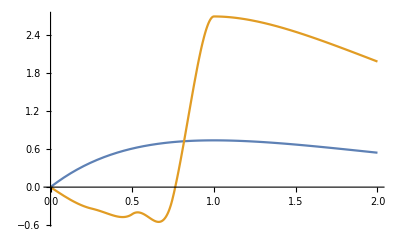

```mathematica
ψ4=normalN[ψψ4[[-1]],4]*ψψ4[[-1]];
Plot[{ψexact[r],renderN[ψ4,4,r]},{r,0,2}]
```

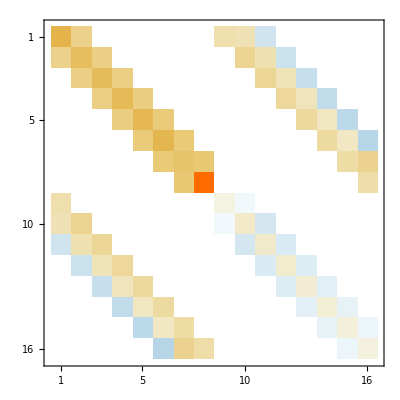

```mathematica
(* N = 8 case *)
PP8=makePorQ[8,Pbar,5/2];
MatrixPlot[PP8]
```

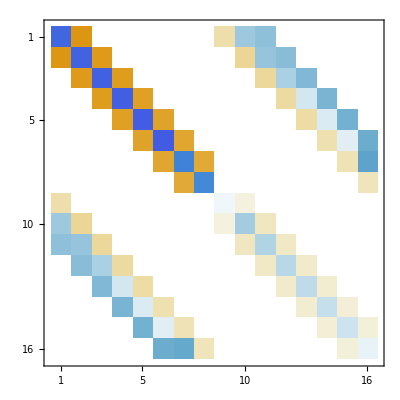

```mathematica
QQ8=makePorQ[8,Qbar,5/2];
MatrixPlot[QQ8]
```

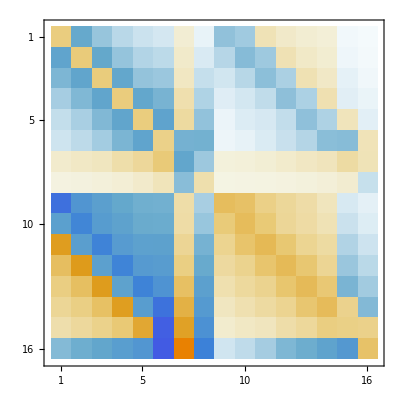

```mathematica
HH8=-Inverse[PP8].QQ8;
MatrixPlot[HH8]
```

```mathematica
{EE8,ψψ8}=Eigensystem[N[HH8,16]];
EE8
ψψ8;
```

{2568.133243794743,2155.208096398677,1732.05684659865,1358.702721489562,1044.960776396346,748.7804414463465+45.8600840269894 ⅈ,748.7804414463465-45.8600840269894 ⅈ,621.2175801016007,422.0704160959392,-326.8420620648769,271.448975045721,-159.2771157471047,153.0696671218193,66.11157184309878,13.14160992692503,5.537963403726692}

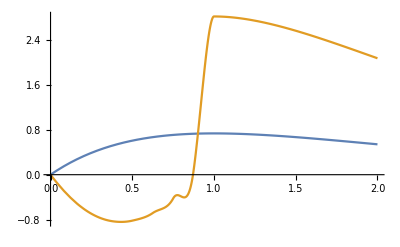

```mathematica
ψ8=normalN[ψψ8[[-1]],8]*ψψ8[[-1]];
Plot[{ψexact[r],renderN[ψ8,8,r]},{r,0,2}]
```